# Lecture 8 - Gauss’s Law

### A Puzzle...

Example
Consider an infinite number of identical point charges q are placed on the x-axis at x=1, x=2, x=3... What is the electric field at the origin?

Solution
Adding the effects of each point charge yields

E⃗=(-x̂)k q (1/1^2+1/2^2+1/3^2+···)

one of the most famous mathematical series. The term in parentheses equals π^2/6. An incredibly elegant geometric proof of that relation can be found using this unbelievably clever method to compute this sum! □

Example
Calculate the potential energy, per ion, for an infinite 1D ionic crystal with separation a; that is, a row of equally spaced charges of magnitude e and alternating sign. 
Hint: The power-series expansion of Log[1+x] may be of use.

Solution
Suppose the array is built inwards from the left (that is, from negative infinity) as far as a particular ion. To add the next positive ion on the right, the amount of external work required equals

-(k e^2)/a+(k e^2)/(2a)-(k e^2)/(3a)+···=-(k e^2)/a(1-1/2+1/3+···)

The terms in parenthesis look remarkably similar to the Taylor series of Log[1+x] when x=1. (What is the Taylor series of Log[1+x]? ⅆ/ⅆx Log[1+x]=1/(1+x)=1-x+x^2-···, and integrating both sides yields Log[1+x]=x-x^2/2+x^3/3-···, since the right hand side is a polynomial expansion, it is also the Taylor series of Log[1+x]. This Taylor series is converging for -1<x≤1 (with convergence on -1<x<1 assured by the alternating series test)). Therefore the work required to bring this charge in equals -(k e^2)/aLog[2], which equals the energy of the infinite chain per ion.

The addition of further particles on the right doesn’t affect the energy involved in assembling the previous ones, so this result is indeed the energy per ion in the entire infinite (in both directions) chain. The result is negative, which means that it requires energy to move the ions away from each other. This makes sense, because the two nearest neighbors are of opposite sign.

Note that this is an exact result! It does not assume that a is small. Getting such a nice closed form is much more difficult in 2 and 3 dimensions. □

### Theory

#### Visualizing the Electric Field (Extended)

Always remember that electric field lines extend in all three dimensions! Any 2D representations are inherently limited.

In version 11, Mathematica released some interesting new functions to help visualize 3D vector fields (i.e. electric fields), including SliceVectorPlot3D. Here we plot a positive (red) point charge interacting with a negative (blue) point charge. You can slice the plots any way that you want. As is usually the case with 3D graphics, these work best if you open them up in Mathematica and interact with them by mouse-clicking and dragging your cursor around.

```mathematica
{pt1,pt2}={{-1,-1,0},{1,1,0}};
ElectroStaticPotential[ql_,pl_,r_]:=Sum[ql[[i]]/Norm[r-pl[[i]]],{i,Length[ql]}];
v=Simplify[ElectroStaticPotential[{1,-1},{pt1,pt2},{x,y,z}],{x,y,z}∈Reals];
field=-Grad[v,{x,y,z}];
centerPlot@Grid[Partition[Table[Show[SliceVectorPlot3D[Clip[field],sl,{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Scientific",ImageSize->250,Boxed->False,Axes->False],Graphics3D[{PointSize[0.03],Red,Point[pt1],Blue,Point[pt2]}]],{sl,{"CenterPlanes","XStackedPlanes","CenterSphere","CenterCutSphere"}}],2],Spacings->{-1,-3}]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

#### Electric Field Lines

People often depict electric fields using electric field lines. For example, consider the electric field lines of a particle with charge +3 and another particle with charge -1.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Often times people use these diagrams to visualize vector fields because the field line density is proportional to the magnitude of the electric field. However, you should be aware that this statement is only true in 3 dimensions! For example, consider a single point charge q with N field lines pointing radially outwards. The density of these field lines at a sphere of radius r from the point charge will be N/(4π r^2), which is the correct 1/r^2 behavior of the electric field. But when we draw these field lines, we do so in 2D, and on our paper the field lines have density N/(2π r), which does not exhibit the 1/r^2 nature of the electric field. So field lines are good for approximately visualizing a situation, but do not try to use them to calculate hard numbers.

#### Advanced Section: Escaping Field Lines

Example
Charges 2q and −q are located on the x-axis at x=0 and x=a, respectively.
1. Find the point on the x-axis where the electric field is zero, and make a rough sketch of some field lines.
2. You should find that some of the field lines that start on the 2q charge end up on the −q charge, while others head off to infinity. Consider the field lines that form the cutoff between these two cases. At what angle (with  respect to the x-axis) do these lines leave the 2q charge? Hint: Draw a wisely chosen Gaussian surface that mainly follows these lines.

Solution
1. It is a simple exercise to show that the desired point with E=0 satisfies x>a. Equating the magnitudes of the electric field from the 2q and -q charges,

(2k q)/x^2=(k q)/(x-a)^2

yields the solution

x=(2+√2)a

Some field lines are shown below. Note that the field points in four different directions near the E=0 point. This is consistent with the fact that the zero vector is the only vector that can simultaneously point in different directions.

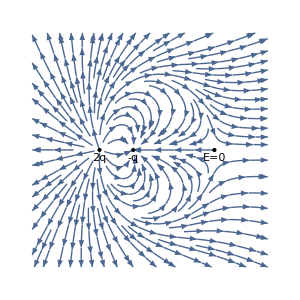

```mathematica
centerPlot@With[{a=1},Show[StreamPlot[{(a-x)/(((a-x)^2+y^2)^(3/2))+(2 x)/((x^2+y^2)^(3/2)),-y/(((a-x)^2+y^2)^(3/2))+(2 y)/((x^2+y^2)^(3/2))},{x,-2,5},{y,-3,3},Frame->False,ImageSize->300],Graphics[{Point[{{0,0},{a,0},{(2+√2)a,0}}],Text["2q",{0,-0.2}],Text["-q",{1,-0.2}],Text["E=0",{2+√2,-0.2}]}]]]
```

2. Consider a field line that emerges from the 2q charge and ends up at the x=(2+√2)a point where the field is zero. (There are actually no field lines that end up right at this point, but we can pick a line infinitesimally close.) Field lines that emerge at a smaller angle (with respect to the x-axis) end up at the -q charge, and field lines that emerge at a larger angle end up at infinity.

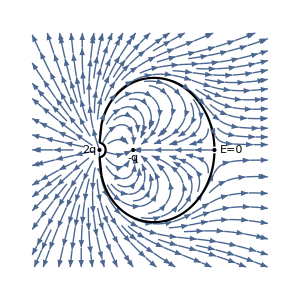

```mathematica
With[{a=1},
{c1,c2}={x,y}/.First@NDSolve[{x'[t]==(a-x[t])/(((a-x[t])^2+y[t]^2)^(3/2))+(2 x[t])/((x[t]^2+y[t]^2)^(3/2)),y'[t]==-y[t]/(((a-x[t])^2+y[t]^2)^(3/2))+(2 y[t])/((x[t]^2+y[t]^2)^(3/2)),x[0.]==0.0,y[0.]==0.001},{x,y},{t,0.,160.}];

(* We want to leave a bit of room around the origin, so we won't show the path around there *)
min=0.001;

centerPlot@Show[StreamPlot[{(a-x)/(((a-x)^2+y^2)^(3/2))+(2 x)/((x^2+y^2)^(3/2)),-y/(((a-x)^2+y^2)^(3/2))+(2 y)/((x^2+y^2)^(3/2))},{x,-2,5},{y,-3,3},Frame->False,ImageSize->300],Graphics[{Point[{{0,0},{a,0},{(2+√2)a,0}}],Text["2q",{-0.3,0}],Text["-q",{1,-0.2}],Text["E=0",{2+√2+0.5,0}]}],ParametricPlot[{{c1[t],c2[t]},{c1[t],-c2[t]}},{t,min,160},PlotStyle->Black],ParametricPlot[Norm@{c1[min],c2[min]}{Cos[θ],Sin[θ]},{θ,-π/2,π/2},PlotStyle->Black]]
]
```

Consider the Gaussian surface indicated in the figure above whose surface is formed by rotating the black curve around the x-axis. This surface follows the field lines except very close to the 2q charge, where it takes the form of a small spherical cap. The total charge enclosed within this surface is simply -q, so from Gauss’s law there must be an electric field flux of q/ϵ_0 pointing into this surface. By construction, the only place there is flux is the spherical cap, so all of the q/ϵ_0 flux must occur there. But the total flux emanating from the charge 2q is (2q)/ϵ_0, so the spherical cap must represent half of the total area of a small sphere surrounding the charge 2q. (Very close to the 2q charge, that charge dominates the electric field, so the field is essentially spherically symmetric.) The cap must therefore be a hemisphere, so the desired angle is 180°.

If the charges take on the more general values of N q and -q, then the spherical cap represents 1/N of the complete sphere. So the task is to find the angle subtended by a cap with 1/N of the total area. One nice case is N=4, which leads to an angle of π/3 (or 60°), as shown by the following integral: ∫_0^(2π) ∫_0^(π/3) R^2 Sin[θ]ⅆθⅆϕ=π R^2 (which is one fourth the surface area of a sphere). □

#### Math Background: What is a Surface Integral?

We are already familiar with surface integrals of scalar functions. For example, the surface area of a sphere with radius R centered at the origin is given by

∫_surface ⅆa=∫_0^(2π) ∫_0^π R^2 Sin[θ]ⅆθⅆϕ=4π R^2

Although we use spherical coordinates in this particular problem, we could also have used Cartesian coordinates (with ⅆa=ⅆxⅆy) or any other coordinate system.

More generally, suppose we are given a function f[θ,ϕ] defined everywhere on the surface of the spherical shell of radius R. What is the integral of f[θ,ϕ] across the entire spherical shell? This requires a very minor modification to the formula above, namely,

∫_surface f[θ,ϕ]ⅆa=∫_0^(2π) ∫_0^π f[θ,ϕ]R^2 Sin[θ]ⅆθⅆϕ

We would need to know the specific function f[θ,ϕ] to explicitly evaluate this integral, but we observe that the surface area is merely a specific case of Equation (TextNumbered) with f[θ,ϕ]=1 everywhere on the sphere.

Lastly, rather than being given a scalar function f[θ,ϕ], we could be given a vector function F⃗[θ,ϕ] defined everywhere on the sphere. In such a case, we define the surface integral to be

∫_surface F⃗[θ,ϕ]·ⅆ a⃗=∫_surface (F⃗[θ,ϕ]·ⅆ â)ⅆa

No need to panic! The right hand side is simply the same surface integral from Equation (TextNumbered), except that now the scalar function is the dot product of two vectors. The first vector F⃗[θ,ϕ] is the function that you are integrating over the sphere. The second vector ⅆ â is a unit vector of an infinitesimal patch in the direction normal to the surface. On the sphere, the unit normal vector at any point is given by ⅆ â=r̂, so that we can write the surface integral as

∫_surface (F⃗[θ,ϕ]·ⅆ â)ⅆa=∫_0^(2π) ∫_0^π (F⃗[θ,ϕ]·r̂)R^2 Sin[θ]ⅆθⅆϕ

For closed surfaces, we take the unit normal to be pointing outwards by convention. For open surfaces, you can arbitrarily choose between the two possible directions that the unit vector can point (if you switch, it will flip the sign of the surface integral).

Usually, we will be working in setups where the unit normal vector is obvious. For example, if we have a sheet in the x-y plane, then the unit normal vector will be ẑ (or -ẑ, you can choose either as long as you are consistent throughout your surface integral) at all points. Similarly, if we have a cylinder whose axis lies on the z-axis, then the unit normal vector at its top cap will be ẑ (remembering that unit normal vectors point outwards for closed surfaces) and -ẑ at its bottom cap. Finally, in cylindrical coordinates (ρ,θ,z), the unit vector will be ρ̂ for all points along the curved surface of the cylinder.

#### Gauss’s Law

An incredibly useful and beautiful result, Gauss’s Law is definitely worth memorizing! Here we write it for a discrete and continuous charge distribution.

The integral ∫E⃗·ⅆ a⃗ over the surface, equals 1/ϵ_0 times the total charge enclosed by the surface,

∫E⃗·ⅆ a⃗=1/ϵ_0∑_j q_j=1/ϵ_0∫ρ ⅆv

For a combination of both (for example, a point charge near an infinite sheet), the Principle of Superposition tells us that we sum over the discrete charges and integrate over the charge distributions within our surface.

Example
An infinite line of charge with uniform charge density λ lies on the z-axis. Determine:

The direction of the electric field at any point

The magnitude of the electric field at any point

Double check this result using both Gauss’s Law and straight-up integration

Solution
By symmetry, the electric field must point radially outwards from the line of charge.

```mathematica
vectors1=Flatten[Table[Arrow[{{x,0.5Cos[θ],0.5Sin[θ]},{x,0.5Cos[θ],0.5Sin[θ]}+1.2{0,Cos[θ],Sin[θ]}}],{θ,π/4,2π,π/4},{x,-10,10,4}],1];
vectors2=Flatten[Table[Arrow[{{x,2Cos[θ],2Sin[θ]},{x,2Cos[θ],2Sin[θ]}+1.5{0,0.5Cos[θ],0.5Sin[θ]}}],{θ,π/4,2π,π/4},{x,-10,10,4}],1];
vectors3=Flatten[Table[Arrow[{{x,Cos[θ],Sin[θ]},{x,Cos[θ],Sin[θ]}+{0,Cos[θ],Sin[θ]}}],{θ,π/4,2π,π/4},{x,-1.8,1.8,1.8}],1];
pts=Prepend[Table[{{3,0,0}+0.8{0,Cos[θ],Sin[θ]},{4,0,0}+0.8{0,Cos[θ],Sin[θ]}},{θ,π/4,2π,π/4}],{{3,0,0},{4,0,0}}];
vectors4=Join[Arrow/@pts,Arrow/@-pts];
centerPlot@Manipulate[
Graphics3D[{Line[{{-10,0,0},{10,0,0}}],{If[showCylinder,Opacity[0.5],Sequence@@{Opacity[0],EdgeForm[]}],Cylinder[3{{-1,0,0},{1,0,0}}]},{If[!showField,Opacity[0]],Darker@Blue,Arrowheads[0.02],vectors1,vectors2,Text[font["E⃗",Bold],{-2,0,3.5}]},{If[!showNormal,Opacity[0]],Darker@Darker@Green,Arrowheads[0.02],vectors3,vectors4,Text[font["a⃗",Bold],{1,0,3.5}]}},Boxed->False,ImageSize->{360.,194.91397659393655},ViewAngle->0.14888267427070792,ViewCenter->{{0.5,0.5,0.5},{0.5467130004557068,0.5440035935644545}},ViewPoint->{-1.9231525921344226,-2.6424566066600046,0.8768735309527532},ViewVertical->{-0.19563003881240032,-1.0847645695350805,2.9894575357366864}]
,{{showCylinder,True,"Cylinder"},{True,False}},{{showField,True,Row[{"Show ",font["E⃗",Italic]}]},{True,False}},{{showNormal,False,Row[{"Show ",font["a⃗",Italic]}]},{True,False}}]
```

To determine the magnitude of the electric field, we use a Gaussian cylinder (the object whose surface we will integrate over) whose axis lies on the line of charge and calculate ∫E⃗·ⅆ a⃗ along this cylinder. Since E⃗ points radially, E⃗·ⅆ a⃗=0 along the (flat) top and bottom of the cylinder, and by radial symmetry, E⃗·ⅆ a⃗=E[r] ⅆa will be a constant value everywhere along the cone (where E[r] is the magnitude of the electric field at a distance r from the wire). Therefore, Gauss's Law yields

∫E⃗·ⅆ a⃗=E[r]∫ⅆa=E[r] (2π r L)=(λ L)/ϵ_0

which yields

E[r]=λ/(2π r ϵ_0)

Alternatively, we could have computed this value by straight-up integration, choosing the radial component of the electric field

```mathematica
centerPlot@-Graphics-
```

-Graphics-

E[r]=∫_(-∞)^∞ (k λⅆx)/(x^2+r^2)r/((x^2+r^2)^(1/2))
=((k λ x)/(r (x^2+r^2)^(1/2)))_(x=-∞)^(x=∞)
=(2k λ)/r
=λ/(2π r ϵ_0)

This yields the same result as above, but after significantly more work. □

#### A Note about Symmetry

The key to the last problem was proving that for a line of charge lying on the x-axis, the electric field E⃗=E[r] r̂ points radially away from the wire. Let’s prove this explicitly.

If the infinitely long wire lies along the x-axis, then the points on the wire are given by (x,0,0) where x∈(-∞,∞). Let us consider the electric field at a point (0,0,z), and let us call the electric field E⃗=⟨E_x,E_y,E_z⟩.

```mathematica
opts={Boxed->False,ImageSize->{370.50321380507387,170.65175936743},ImageSizeRaw->Automatic,ViewPoint->{1.3726050943998032,-2.823465704822308,1.2625358088070109},ViewVertical->{0.259769130577393,-3.481230319311825,2.6123271695549386}};
centerPlot@Graphics3D[{Line[{{-10,0,0},{10,0,0}}],{Arrowheads[0.02],Arrow[{{-8,0,3},{-8,0,3}+#}&/@{{2,0,0},{0,2,0},{0,0,2}}],Text[font@"x̂",{-8,0,3}+{2.5,0,0}],Text[font@"ŷ",{-8,0,3}+{0,2.5,0}],Text[font@"ẑ",{-8,0,3}+{0,0,2.5}]},{Darker@Blue,Dashed,Line[{{0,0,0},{0,0,3}}],PointSize[0.02],Point[{0,0,3}],Text[font["(0,0,z)"],{0,0,3}+{-1,0,0.7}]},{Darker@Darker@Green,Arrow[{{0,0,3},2{1,0.5,3.3}}],Text[font["E⃗=⟨E_x,E_y,E_z⟩"],{1,0.5,4.8}+{2.5,0,-0.4}]}},Sequence@@opts]
```

-Graphics3D-

First, let us flip the setup along the x=0 as shown below, which means that every point (and every vector) goes from (x,y,z)→(-x,y,z). Therefore the electric field will go from ⟨E_x,E_y,E_z⟩→⟨-E_x,E_y,E_z⟩, shown by the solid arrow → dashed arrow. However, since every point (x,0,0) on the line of charge goes to another point (-x,0,0) on the line of charge, and the point of interest (0,0,z)→(0,0,z) does not change, the physical setup of the problem remains exactly the same. Therefore, the electric field before and after the reflection must be the same, and this is only possible if E_x=0.

```mathematica
opts={Boxed->False,ImageSize->{378.02791624086524,273.06656504407266},ImageSizeRaw->Automatic,ViewPoint->{1.271505463819623,-2.871951306570197,1.2590351655798155},ViewVertical->{0.3288463279153931,-1.4197523434276087,1.0738707165403063}};
centerPlot@Graphics3D[{Line[{{-10,0,0},{10,0,0}}],{Arrowheads[0.02],Arrow[{{-8,0,3},{-8,0,3}+#}&/@{{2,0,0},{0,2,0},{0,0,2}}],Text[font@"x̂",{-8,0,3}+{2.5,0,0}],Text[font@"ŷ",{-8,0,3}+{0,2.5,0}],Text[font@"ẑ",{-8,0,3}+{0,0,2.5}]},{Darker@Blue,Dashed,Line[{{0,0,0},{0,0,3}}],PointSize[0.02],Point[{0,0,3}],Text[font["(0,0,z)"],{0,0,3}+{-1.4,0,0.3}]},{Darker@Darker@Green,Arrow[{{0,0,3},2{1,0.5,3.3}}],Dashed,Arrow[{{0,0,3},2{-1,0.5,3.3}}],Text[font["E⃗=⟨E_x,E_y,E_z⟩"],{1,0.5,4.8}+{2.5,0,-0.4}]},{Opacity[0.5],Orange,Polygon[5{{0,1,1},{0,1,-1},{0,-1,-1},{0,-1,1}}]}},Sequence@@opts]
```

-Graphics3D-

Similarly, consider a reflection about the y=0 plane, so that every point goes from (x,y,z)→(x,-y,z). Therefore the electric field will go from ⟨0,E_y,E_z⟩→⟨0,-E_y,E_z⟩. Each point on the line of charge will not be changed (x,0,0)→(x,0,0), and similarly the point of interest will not change (0,0,z)→(0,0,z), so that once again the physical setup is the same and hence the electric field must be the same. This can only happen in E_y=0.

```mathematica
opts={Boxed->False,ImageSize->{347.708482478922,240.96520671521944},ImageSizeRaw->Automatic,ViewPoint->{1.3026101827432501,-2.8883345617849723,1.1877416263699858},ViewVertical->{0.2752734776870031,-2.2111349290472324,1.3693120642677563}};
centerPlot@Graphics3D[{Line[{{-10,0,0},{10,0,0}}],{Arrowheads[0.02],Arrow[{{-8,0,3},{-8,0,3}+#}&/@{{2,0,0},{0,2,0},{0,0,2}}],Text[font@"x̂",{-8,0,3}+{2.5,0,0}],Text[font@"ŷ",{-8,0,3}+{0,2.5,0}],Text[font@"ẑ",{-8,0,3}+{0,0,2.5}]},{Darker@Blue,Dashed,Line[{{0,0,0},{0,0,3}}],PointSize[0.02],Point[{0,0,3}],Text[font["(0,0,z)"],{0,0,3}+{-1.5,0,-0.7}]},{Darker@Darker@Green,Arrow[{{0,0,3},2{0,1.2,3.3}}],Dashed,Arrow[{{0,0,3},2{0,-1.2,3.3}}],Text[font["E⃗=⟨0,E_y,E_z⟩"],{1,0.5,4.8}+{2.5,0,0.85}]},{Opacity[0.5],Orange,Polygon[5{{1,0,1},{1,0,-1},{-1,0,-1},{-1,0,1}}]}},Sequence@@opts]
```

-Graphics3D-

We conclude that at the point (0,0,z), the electric field point straight up (i.e. radially away) from the line of charge. We can generalize this result to find the direction of the electric field at an arbitrary point (x,y,z) using symmetry. First, we note that because the wire is infinitely long, translating along the x-direction cannot change the electric field, since we could equally well have defined our origin at some other point (X,0,0) and the physical setup would be identical to that found above, so that the electric field at (X,0,z) must point in the ẑ direction. Finally, we use the rotational symmetry of the setup (i.e. rotating our coordinate system about the x-axis) to find that the electric field at any point (x,y,z) points radially outward from the wire in the direction ⟨0,y,z⟩.

### Problems

#### Field from a Cylindrical Shell

Example
Consider a charge distribution in the form of an infinitely long hollow circular cylinder (like a long charged pipe) of radius R. If the cylinder has uniform charge per unit area σ, what is the electric field inside and outside the cylinder?

Solution
The electric field inside the cylinder must be pointing radially about the axis of symmetry. Therefore, using a Gaussian surface of a small cylinder with radius r<R and length l placed along the axis of the large cylinder, we find that

E (2π r l)=q_in/ϵ_0=0

because there is no charge inside the cylindrical shell. Thus, E=0 for all r<R.

The electric field outside the cylinder is found using a the same Gaussian surface but with r>R so that

E (2π r l)=q_in/ϵ_0=(2π R l σ)/ϵ_0

or equivalently E=R/r σ/ϵ_0. Since the charge per unit length on the cylindrical shell equals 2π R σ, E=(2π R σ)/(2π r ϵ_0) so that the electric field outside the cylinder is the same as if all of the charge was concentrated at on the axis of the cylinder.

These results are very interesting, but let me point out one subtlety in this result. If you ask for the electric field E[r] as a function of the radial distance r from the cylindrical shell, then starting at ∞ and coming towards the axis the answer will be

E[r]=Piecewise[{{R/r σ/ϵ_0, r>R}, {0, r<R}}]

This implies that at r=R, there is a discontinuity; the value of E[r]→σ/ϵ_0 from the outside of the cylindrical shell and E[r]→0 from the inside of the shell. This begs the question, what exactly is the electric field at r=R? As we will see from the electric field of an infinite plane, the answer will be E[R]=σ/(2 ϵ_0), and you are encouraged to do the explicit calculation yourself! For now, we note that E[R] is the average of the values two limits of E[r] from inside and outside the cylindrical shell. □

#### Extra Problem: Field from a Cylindrical Shell, Right and Wrong

Example
Find the electric field outside a uniformly charged hollow cylindrical shell with radius R and charge density σ, an infinitesimal distance away from it. Do this in the following two ways:

1. Slice the shell into parallel infinite rods, and integrate the field contributions from all the rods. You should obtain the incorrect result of σ/(2 ϵ_0).

2. Why isn't the result correct? Explain how to modify it to obtain the correct result of σ/ϵ_0. Hint: You could very well have performed the above integral in an effort to obtain the electric field an infinitesimal distance inside the cylinder, where we know the field is zero. Does the above integration provide a good description of what's going on for points on the shell that are very close to the point in question?

3. Confirm that the result equals σ/ϵ_0 by straight up integration assuming that the point is a finite distance z away from the center of the cylinder. What happens when z<R, z=R, and z>R?

Solution
1. Let the rods be parameterized by the angle θ as shown in the diagram below.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

The width of a rod is R ⅆθ, so its effective charge per unit length is λ=σ (Rⅆθ). The rod is a distance 2R Sin[θ/2] from the point P in question, which is infinitesimally close to the top of the cylinder. Only the vertical component of the field from the rod survives, and this brings in a factor of Sin[θ/2]. Using the fact that the field from a rod is λ/(2π ϵ_0 r), we find that the field at the top of the cylinder is (incorrectly)

2∫_0^π (σ R ⅆθ)/(2π ϵ_0(2R Sin[θ/2]))Sin[θ/2]=σ/(2π ϵ_0)∫_0^π ⅆθ=σ/(2 ϵ_0)

Interestingly, we see that for a given angular width of a rod, all rods yield the same contribution to the vertical electric field at P (since the ones further away from it contribute at a better angle).

2. As stated in the problem, it is no surprise that this answer is incorrect, since the same calculation would supposedly yield the field just inside the cylinder too, where it is zero instead of σ/ϵ_0. However, this calculation does yield the average of these two values.

The reason why the calculation is invalid is that it doesn’t correctly describe the field due to rods very close to the given point, that is, for rods with θ≈0. It is incorrect for two reasons. First, the distance from a rod to the given point is not equal to 2R Sin[θ/2]. Additionally, the field does not point along the line from the rod to the top of the cylinder. It points more vertically, so the extra factor of Sin[θ/2] which we used to pick out the vertical component isn’t valid.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

What is true is that if we remove a thin strip from θ=-ϕ/2 to θ=ϕ/2 (for very small ϕ≪1) at the top of the cylinder, then the above integral is valid for the remaining part of the cylinder. In other words, the electric field due to the remaining cylinder will be (2π-ϕ)/(2π)σ/(2 ϵ_0)≈σ/(2 ϵ_0) since we can make (2π-ϕ)/(2π) arbitrarily close to 1. By superposition, the total field of the entire cylinder in this field of σ/(2 ϵ_0) plus the field due to the thin strip at the top. But if the point in question is infinitesimally close to the cylinder, then the thin strip will look like an infinite plane, the field of which we know is σ/(2 ϵ_0). The desired total field is then

E_outside=E_(cylinder minus strip)+E_strip=σ/(2 ϵ_0)+σ/(2 ϵ_0)=σ/ϵ_0

E_inside=E_(cylinder minus strip)-E_strip=σ/(2 ϵ_0)-σ/(2 ϵ_0)=0

where the minus sign in E_inside comes from the fact that E_strip (like an infinite sheet) points in different directions inside and outside the cylinder.

Technical note: We have two infinitesimally small quantities in this problem: the width ϕ of the strip that we are removing from the cylinder and the infinitesimal distance of the point P from the cylinder. You may (or at least should) be wondering which of these two infinitesimally small quantities is smaller. This is an important point to keep track of - if you are blasé about the matter and simply send both quantities to 0 without regard, you could end up with wrong results! In this problem, we want for the distance from P to the cylinder to be smaller, and indeed that is the case. For we first picked a small ϕ (which we can make as small as we like) and then we considered a point P which was essentially touching the cylinder but on the outside; you can think of this as once you fix ϕ, you bring P in extremely close to the cylinder (and therefore extremely close to the thin strip).

3. Orient the cylinder’s axis to lie on the y-axis and consider the electric field at the point (0,0,z).

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Define the distance from the wire at angle θ to the point (0,0,z) to be r, which by the Law of Cosines equals r^2=R^2+z^2-2R z Cos[θ]. Using the charge density λ=σ (Rⅆθ), the electric field λ/(2π ϵ_0 r) from an infinite wire, and the z-component (z-R Cos[θ])/r of the electric field,

E=∫_0^(2π) (R σⅆθ)/(2π ϵ_0 r)(z-R Cos[θ])/r=(R σ)/(2π ϵ_0)∫_0^(2π) (z-R Cos[θ])/(R^2+z^2-2R z Cos[θ])ⅆθ

This integral is not super-difficult to evaluate, but care must be taken as to whether z<R, z=R, or z>R. The full result is given by

E=R/z(σ (1-Sign[R-z]))/(2 ϵ_0)

```mathematica
Integrate[(R σ)/(2π ϵ0)(z-R Cos[θ])/(R^2+z^2-2R z Cos[θ]),{θ,0,2π},Assumptions->0<ϵ0&&0<σ&&0<R&&0<z]
```

-(R σ (-1+Sign[R-z]))/(2 z ϵ0)

In other words,

E=Piecewise[{{0, z<R}, {σ/(2 ϵ_0), z=R}, {R/z σ/ϵ_0, z>R}}]

We see that when we approach the surface of the cylinder from the inside E=0, whereas when we approach it from the outside, E=R/z σ/ϵ_0→σ/ϵ_0. The electric field on the actual surface equals the average of these two values, E=σ/(2 ϵ_0). □

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
RawBoxes@CounterBox["TextNumbered","eq1"]
```

TextNumbered

Figure for Gauss’s Law handout

```mathematica
(*font["dâ",40,Italic,Darker@Darker@Green]*)
```

```mathematica
(*size=5;
arrows={#,2#}&/@{{1,0,0},{0,1,0},{0,0,1}};
arrows2=Flatten[Table[{{1,y,z},{2,y,z}},{y,-6,0,2},{z,-2,4,2}],1];
opts={Boxed->False,ImageSize->{141.66861218830388,400.},ViewAngle->0.13714372734467772,ViewCenter->{{0.5,0.5,0.5},{0.5819836217566133,0.6028976297419993}},ViewPoint->{1.5567853741422026,-2.930776533049194,0.6610357117320341},ViewVertical->{0.8444285030529095,-0.4402265175065663,0.9546346879118492}};
Show[Graphics3D[{{Opacity[0.6],Polygon[{{0,size,size},{0,size,-size},{0,-size,-size},{0,-size,size}}]},Line[{{{-1,-1,1},{1,-1,1},{1,1,1},{-1,1,1},{-1,-1,1},{-1,-1,-1},{1,-1,-1},{1,1,-1},{-1,1,-1},{-1,-1,-1}},{{1,-1,1},{1,-1,-1}},{{1,1,1},{1,1,-1}},{{-1,1,1},{-1,1,-1}}}],Text[font@"2s",{0.35,-1,0.7}],Arrowheads[0.02],Darker@Blue,Arrow[arrows2],Darker@Darker@Green,Arrow[arrows],Arrow[-arrows[[2;;]]]}],ParametricPlot3D[{1,y,z},{y,-1,1},{z,-1,1},Mesh->False],ParametricPlot3D[{x,1,z},{x,-1,1},{z,-1,1},Mesh->False],ParametricPlot3D[{x,y,1},{x,-1,1},{y,-1,1},Mesh->False],
ParametricPlot3D[{-1,y,z},{y,-1,1},{z,-1,1},Mesh->False],ParametricPlot3D[{x,-1,z},{x,-1,1},{z,-1,1},Mesh->False],ParametricPlot3D[{x,y,-1},{x,-1,1},{y,-1,1},Mesh->False],opts]*)
```

```mathematica
(*arrows=Table[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},1.3{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}},{θ,0,π,π/4},{ϕ,0,2π,π/4}];
arrows2=Table[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},1.3{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}},{θ,π/8,π,π/4},{ϕ,0,2π,π/4}];
Show[Graphics3D[{Arrowheads[0.025],Darker@Darker@Green,Arrow/@arrows,Darker@Blue,Arrow/@arrows2}],ParametricPlot3D[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},Mesh->None,PlotPoints->50,Axes->None],{Boxed->False,ImageSize->{309.7801279329346,293.6446225336725},ViewAngle->0.2878623021445321,ViewCenter->{{0.5,0.5,0.5},{0.500636348816231,0.5010328288345949}},ViewPoint->{1.114572905699343,-2.994104807940617,1.114927637538779},ViewVertical->{0.06712601747692656,-0.2877095303005277,0.9553624045104231}}]*)
```

```mathematica
(*vectors1=Flatten[Table[Arrow[{{x,0.5Cos[θ],0.5Sin[θ]},{x,0.5Cos[θ],0.5Sin[θ]}+1.2{0,Cos[θ],Sin[θ]}}],{θ,π/4,2π,π/4},{x,-10,10,4}],1];
vectors2=Flatten[Table[Arrow[{{x,2Cos[θ],2Sin[θ]},{x,2Cos[θ],2Sin[θ]}+1.5{0,0.5Cos[θ],0.5Sin[θ]}}],{θ,π/4,2π,π/4},{x,-10,10,4}],1];
vectors3=Flatten[Table[Arrow[{{x,Cos[θ],Sin[θ]},{x,Cos[θ],Sin[θ]}+{0,Cos[θ],Sin[θ]}}],{θ,π/4,2π,π/4},{x,-1.8,1.8,1.8}],1];
pts=Prepend[Table[{{3,0,0}+0.8{0,Cos[θ],Sin[θ]},{4,0,0}+0.8{0,Cos[θ],Sin[θ]}},{θ,π/4,2π,π/4}],{{3,0,0},{4,0,0}}];
vectors4=Join[Arrow/@pts,Arrow/@-pts];
Manipulate[
Show[Graphics3D[{{If[showCylinder,Opacity[0.5],Sequence@@{Opacity[0],EdgeForm[]}],Cylinder[3{{-1,0,0},{1,0,0}}]},{If[!showField,Opacity[0]],Darker@Blue,Arrowheads[0.02],vectors1,vectors2,Text[font["E⃗",Bold],{-2,0,3.5}]},{If[!showNormal,Opacity[0]],Darker@Darker@Green,Arrowheads[0.02],vectors3,vectors4,Text[font["a⃗",Bold],{1,0,3.5}]}},{Boxed->False,ImageSize->{360.,194.91397659393655},ViewAngle->0.06747277398162507,ViewCenter->{{0.5,0.5,0.5},{0.5467130004557068,0.5440035935644545}},ViewPoint->{-1.5841872074601642,-2.8801460160923265,0.8031872868186322},ViewVertical->{-0.1685774941421026,-1.2283027956237589,2.963213981461439}}],ParametricPlot3D[{x,Cos[θ],Sin[θ]},{θ,0,2 π},{x,-3,3},Mesh->None,PlotStyle->Opacity[1]],ParametricPlot3D[{-3,r Cos[θ],r Sin[θ]},{θ,0,2 π},{r,0,1},Mesh->None,PlotStyle->Opacity[1],PerformanceGoal->"Quality"],ParametricPlot3D[{3,r Cos[θ],r Sin[θ]},{θ,0,2 π},{r,0,1},Mesh->None,PlotStyle->Opacity[1],PerformanceGoal->"Quality"]]
,{{showCylinder,False,"Cylinder"},{True,False}},{{showField,False,Row[{"Show ",font["E⃗",Italic]}]},{True,False}},{{showNormal,True,Row[{"Show ",font["a⃗",Italic]}]},{True,False}}]*)
```